```mathematica
(* f е с 2 аргумента, въпреки че в нашия конкретен случай зависи само от x. Дефинираме го за общия случай *)
{{f[x_,y_]  := Sin[x^4]Exp[x^2];
h=0.1;u0=0; T=3;
ndsol = NDSolve[{u'[x] == f[x ,0], u[0]==0}, u[x], {x,0,T}];
pl2 = Plot[u[x]/.ndsol, {x, 0 ,3}, PlotRange-> All];


RungeKutta23[f_, u0_, h0_, T_, tol_, maxIter_] := (
h=h0;
y={u0};
mesh={0};
While[Last[mesh] < T,
k1=h f[Last[mesh],Last[y]];
k2 = h f[Last[mesh] + h, Last[y] + k1];
k3=h f[Last[mesh] + 1/2h, Last[y] + 1/4k1 + 1/4k2];
y2= Last[y] + 1/2k1 + 1/2k2;
y3 = Last[y] + 1/6k1 + 1/6k2 + 2/3k3;
(* To do: implement adaptive step choice *)
err = Abs[y2-y3];
h= Power[tol/err, 1/3]*h;
i=0;
While[ err>tol && i<maxIter,
k1=h f[Last[mesh],Last[y]];
k2 = h f[Last[mesh] + h, Last[y] + k1];
k3=h f[Last[mesh] + 1/2h, Last[y] + 1/4k1 + 1/4k2];
y2= Last[y] + 1/2k1 + 1/2k2;
y3 = Last[y] + 1/6k1 + 1/6k2 + 2/3k3;
err = Abs[y2-y3];
h= Power[tol/err, 1/3]*h;
i++;
];
AppendTo[y,y3];
AppendTo[mesh, Last[mesh] + h];
];
Return[Transpose[{mesh, y}]];
);  
tol=10^-5; maxIter=1000;
rk23 = RungeKutta23[f,u0,h,T, tol, maxIter];
lp23 = ListPlot[rk23, PlotStyle->Green, PlotRange->All];
Show[lp23, pl2]
(* от 0-1 може и големи стъпки защото производната е 0, след 2 фунцията се изменя доста, затова ни трябва малка стъпка за да анализираме*)}, {□}}
```

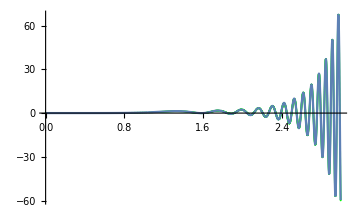
```mathematica
{{Null^8 -Graphics-},{□}}
{{interpolation[xList_, yList_] := (
n = Length[xList];
basis = Table[0,n];
For[i=1, i≤ n, i++,
	numerator = Product[(x - xList[[k]]), {k, Delete[Range[n],i]}];
	denominator = numenator/. -> xList[[i]] (*denomnator e kato numenator no zameni x s x ot i*)
basis[[i]] = numenator/denominator;
];
res = Dot[yList, basis] (* skalarno proizvedenie na vektori - vseki element na ediniq se umnojava po element ot drugiq*)

Return [res];
);}, {□}}
```

{{Null^8 -Graphics-},{□}}

```mathematica
xList={1,2,3};
yList={-3,0,2};
Clear[int];
int[x_] = interpolation[xList, yList]
```